```mathematica
PolyhedronData["TruncatedCuboctahedron"]
```

-Graphics3D-

```mathematica
TruncatedCuboctahedronPts=PolyhedronData["TruncatedCuboctahedron","VertexCoordinates"]//RootReduce//Times[#,2]&//InputForm;
TruncatedCuboctahedronFaces=PolyhedronData["TruncatedCuboctahedron","FaceIndices"]//#-1&//InputForm;
```

```mathematica
ToOpenSCADExpr:=StringReplace[ToString[#],{"Sqrt["->"sqrt(","]"->")","{"->"[","}"->"]"}]&;
ToOpenSCADExpr[TruncatedCuboctahedronPts]
ToOpenSCADExpr[TruncatedCuboctahedronFaces]
```

[[-1, 1 + sqrt(2), -1 - 2*sqrt(2)], [-1, 1 + sqrt(2), 1 + 2*sqrt(2)], [-1, -1 - sqrt(2), -1 - 2*sqrt(2)], [-1, -1 - sqrt(2), 1 + 2*sqrt(2)], [-1, -1 - 2*sqrt(2), 1 + sqrt(2)], [-1, -1 - 2*sqrt(2), -1 - sqrt(2)], [-1, 1 + 2*sqrt(2), 1 + sqrt(2)], [-1, 1 + 2*sqrt(2), -1 - sqrt(2)], [1, 1 + sqrt(2), -1 - 2*sqrt(2)], [1, 1 + sqrt(2), 1 + 2*sqrt(2)], [1, -1 - sqrt(2), -1 - 2*sqrt(2)], [1, -1 - sqrt(2), 1 + 2*sqrt(2)], [1, -1 - 2*sqrt(2), 1 + sqrt(2)], [1, -1 - 2*sqrt(2), -1 - sqrt(2)], [1, 1 + 2*sqrt(2), 1 + sqrt(2)], [1, 1 + 2*sqrt(2), -1 - sqrt(2)], [1 + sqrt(2), -1, -1 - 2*sqrt(2)], [1 + sqrt(2), -1, 1 + 2*sqrt(2)], [1 + sqrt(2), 1, -1 - 2*sqrt(2)], [1 + sqrt(2), 1, 1 + 2*sqrt(2)], [1 + sqrt(2), -1 - 2*sqrt(2), -1], [1 + sqrt(2), -1 - 2*sqrt(2), 1], [1 + sqrt(2), 1 + 2*sqrt(2), -1], [1 + sqrt(2), 1 + 2*sqrt(2), 1], [-1 - sqrt(2), -1, -1 - 2*sqrt(2)], [-1 - sqrt(2), -1, 1 + 2*sqrt(2)], [-1 - sqrt(2), 1, -1 - 2*sqrt(2)], [-1 - sqrt(2), 1, 1 + 2*sqrt(2)], [-1 - sqrt(2), -1 - 2*sqrt(2), -1], [-1 - sqrt(2), -1 - 2*sqrt(2), 1], [-1 - sqrt(2), 1 + 2*sqrt(2), -1], [-1 - sqrt(2), 1 + 2*sqrt(2), 1], [-1 - 2*sqrt(2), -1, 1 + sqrt(2)], [-1 - 2*sqrt(2), -1, -1 - sqrt(2)], [-1 - 2*sqrt(2), 1, 1 + sqrt(2)], [-1 - 2*sqrt(2), 1, -1 - sqrt(2)], [-1 - 2*sqrt(2), 1 + sqrt(2), -1], [-1 - 2*sqrt(2), 1 + sqrt(2), 1], [-1 - 2*sqrt(2), -1 - sqrt(2), -1], [-1 - 2*sqrt(2), -1 - sqrt(2), 1], [1 + 2*sqrt(2), -1, 1 + sqrt(2)], [1 + 2*sqrt(2), -1, -1 - sqrt(2)], [1 + 2*sqrt(2), 1, 1 + sqrt(2)], [1 + 2*sqrt(2), 1, -1 - sqrt(2)], [1 + 2*sqrt(2), 1 + sqrt(2), -1], [1 + 2*sqrt(2), 1 + sqrt(2), 1], [1 + 2*sqrt(2), -1 - sqrt(2), -1], [1 + 2*sqrt(2), -1 - sqrt(2), 1]]

[[43, 41, 16, 18], [13, 5, 2, 10], [33, 35, 26, 24], [7, 15, 8, 0], [19, 17, 40, 42], [11, 3, 4, 12], [25, 27, 34, 32], [1, 9, 14, 6], [44, 22, 23, 45], [38, 28, 29, 39], [47, 21, 20, 46], [37, 31, 30, 36], [8, 18, 16, 10, 2, 24, 26, 0], [1, 27, 25, 3, 11, 17, 19, 9], [40, 47, 46, 41, 43, 44, 45, 42], [34, 37, 36, 35, 33, 38, 39, 32], [14, 23, 22, 15, 7, 30, 31, 6], [4, 29, 28, 5, 13, 20, 21, 12], [45, 23, 14, 9, 19, 42], [34, 27, 1, 6, 31, 37], [40, 17, 11, 12, 21, 47], [39, 29, 4, 3, 25, 32], [43, 18, 8, 15, 22, 44], [36, 30, 7, 0, 26, 35], [46, 20, 13, 10, 16, 41], [33, 24, 2, 5, 28, 38]]

```mathematica
PolyhedronData["TruncatedCuboctahedron","VertexCoordinates"]//Times[#,2]&//{Min[#],Max[#]}&//RootReduce//InputForm//ToOpenSCADExpr[#]&
```

[-1 - 2*sqrt(2), 1 + 2*sqrt(2)]

```mathematica
(* Scale *)
55/(2+4Sqrt[2])//RootReduce//InputForm//ToOpenSCADExpr[#]&
```

(-55 + 110*sqrt(2))/14

```mathematica
vrts=PolyhedronData["TruncatedCuboctahedron","VertexCoordinates"]//RootReduce//Times[#,2]&;
pos=Select[PolyhedronData["TruncatedCuboctahedron","FaceIndices"],Length[#]==8&];
```

```mathematica
(*If pos is an array of element indices that need to be taken from list arr, then actual extract is done by Map with trivial lambda: arr[[#]]& /@ pos, maybe its naiveness explains why there are no special API for that in Mathematica... 
BTW, reverse task API exists - Position
 *)
vrts⟦#⟧&/@pos⟦1⟧
mountSideVTX=Take[#,2]&/@(vrts⟦#⟧&/@pos⟦1⟧)
```

{{1,1+√2,-1-2 √2},{1+√2,1,-1-2 √2},{1+√2,-1,-1-2 √2},{1,-1-√2,-1-2 √2},{-1,-1-√2,-1-2 √2},{-1-√2,-1,-1-2 √2},{-1-√2,1,-1-2 √2},{-1,1+√2,-1-2 √2}}

{{1,1+√2},{1+√2,1},{1+√2,-1},{1,-1-√2},{-1,-1-√2},{-1-√2,-1},{-1-√2,1},{-1,1+√2}}

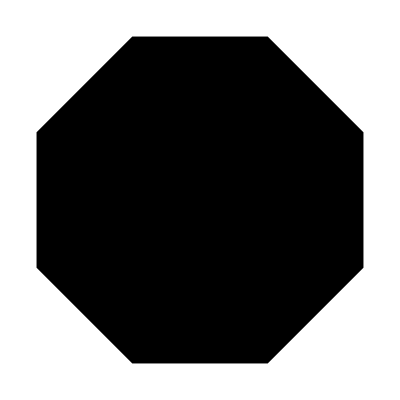

```mathematica
mountSideVTX//Polygon//Graphics
```

```mathematica
ToOpenSCADExpr[mountSideVTX]
```

[[1, 1 + sqrt(2)], [1 + sqrt(2), 1], [1 + sqrt(2), -1], [1, -1 - sqrt(2)], [-1, -1 - sqrt(2)], [-1 - sqrt(2), -1], [-1 - sqrt(2), 1], [-1, 1 + sqrt(2)]]

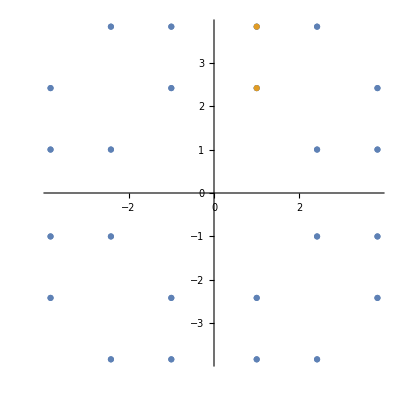

```mathematica
ListPlot[{Take[#,2]&/@vrts,{{1,1+Sqrt[2]},{1,1+2Sqrt[2]}}},AspectRatio->1]
```